```mathematica
NS["plinkinetti_cluster7"]
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons7c\\"
```

C:\Users\pglpm\repositories\plinkinetti\comparisons7c\

```mathematica
logt[x_,a_:1]=Sign[x]*Log[10,1+Abs[x/a]];
ilogt[x_,a_:1]=Sign[x]*(10^(Abs[x/a])-1);
logistic[x_]=1/(1+Exp[-x]);
semilogistic[x_]=1-Exp[-x];
```

```mathematica
pairs=Flatten[Table[{i,j},{i,1,4},{j,i+1,4}],1];npairs=Length[pairs];
names={ln[Style[N,Italic]],Style[γ,Italic],Subscript[Style[γ,Italic],m],Subscript[Style[γ,Italic],v]};
```

```mathematica
names
```

{ln[N],γ,γ_m,γ_v}

```mathematica
data=Import[wd<>"points_mean1jsd.csv"];ndata=Length[data];data[[1;;4]]
```

{{1,2.29152,-12.6621,-3.73813,2.73091},{2,7.0211,-19.3511,3.50068,-6.32137},{3,-0.523288,-11.2757,-0.851212,2.16753},{4,2.66919,-38.441,-44.6178,1.42607}}

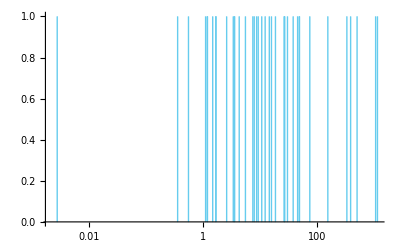

```mathematica
myfontsize=10;fixLogPlots@ListLogLinearPlot[{T@{Exp@data[[;;,2]],Table[0,ndata]},
T@{Exp@data[[;;,2]],Table[1,ndata]}},Filling->{1->{2}},Axes->{True,False},AxesStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],TicksStyle->Thickness[0.002],FillingStyle->{Opacity[1],Thickness[0.001]},PlotStyle->Table[{blue,PointSize[0]},2]]
```

```mathematica
expdf["test"]
```

test.pdf

```mathematica
myfontsize=21;gridp=GraphicsGrid[mfromaboveanddiag@Flatten@Table[If[i==j,ListPlot[{T@{data[[;;,i]],Table[0,ndata]},
T@{data[[;;,i]],Table[1,ndata]}},Filling->{1->{2}},PlotRange->All,Axes->None,Frame->{True,False,False,False},
FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],FrameTicksStyle->Thickness[0.005],FrameLabel->myaxes[{names[[i-1]],""}],FillingStyle->{Opacity[1],Thickness[0.001]},PlotStyle->Table[{purpleblue,PointSize[0]},2],AspectRatio->1,ImageSize->Large],

ListPlot[data[[;;,{i,j}]],PlotRange->All,
PlotMarkers->{"+",Large},PlotStyle->purpleblue,FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],FrameTicksStyle->Thickness[0.005],AspectRatio->1,ImageSize->Large,
Axes->None,Frame->{True,True,False,False},FrameLabel->myaxes[names[[{i-1,j-1}]]]]],{i,2,5},{j,i,5}]];
```

```mathematica
expdf0["clusters_jsd",gridp]
```

clusters_jsd.pdf

```mathematica
logt[-100]//N
```

-2.00432

```mathematica
Reverse@Range[5]
```

{5,4,3,2,1}

```mathematica
ticklist=Join[-10^Reverse@Table[i,{i,0,6}],{0},10^Table[i,{i,0,6}],-5*10^Reverse@Table[i,{i,0,6}],5*10^Table[i,{i,0,6}]];
```

```mathematica
ticks=Thread[{logt[ticklist],ticklist}];
rotticks=Thread[{logt[ticklist],(Rotate[#,Pi/2]&)/@ticklist}];
```

```mathematica
gridpl=GraphicsGrid[mfromaboveanddiag@Flatten@Table[If[i==j,ListPlot[{T@{logt@data[[;;,i]],Table[0,ndata]},
T@{logt@data[[;;,i]],Table[1,ndata]}},
PlotRange->All,Filling->{1->{2}},Axes->None,
FrameTicks->{{None,None},{rotticks,None}},Frame->{True,False,False,False},FrameLabel->myaxes[{names[[i-1]],""}],FillingStyle->{Opacity[1],Thickness[0.001]},PlotStyle->Table[{blue,PointSize[0]},2],AspectRatio->1,ImageSize->Large],

ListPlot[logt@data[[;;,{i,j}]],PlotRange->All,
PlotMarkers->{"+",Large},
FrameTicks->{{ticks,None},{rotticks,None}},FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->"Palatino"],AspectRatio->1,ImageSize->Large,
Axes->None,Frame->{True,True,False,False},FrameLabel->myaxes[names[[{i-1,j-1}]]]]],{i,2,5},{j,i,5}]];
```

```mathematica
expdf0["clusters_jsd_logscale",gridpl]
```

clusters_jsd_logscale.pdf

```mathematica
Min[logt@data[[;;,2]]]
```

-0.905554

```mathematica
PlotLine[T@{Exp@data[[;;,2]],Table[1,ndata]},PlotStyle->PointSize[0.01],PlotRange->All]
```

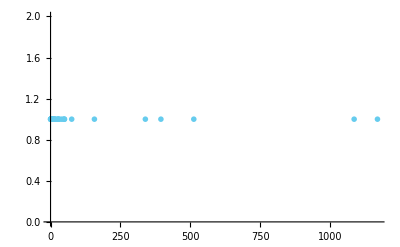

```mathematica
ListPlot[T@{Exp@data[[;;,2]],Table[1,ndata]},PlotStyle->PointSize[0.01],PlotRange->All]
```

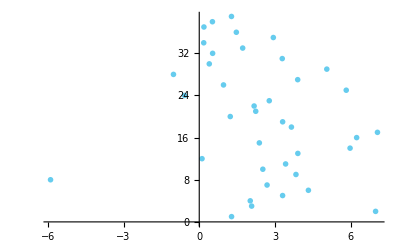

```mathematica
ListPlot[T@{data[[;;,2]],Table[i,{i,ndata}]},PlotStyle->PointSize[0.01],PlotRange->All]
```

```mathematica
myfontsize=15;tab=Table[
plot[i]=Show[{ListPlot[data[[;;,pairs[[i]]+1]],PlotRange->Table[{-50,50},2],
PlotMarkers->{"+",Large},FrameStyle->Directive[Black,myfontsize,Thickness[1/500],FontFamily->"Palatino"],AspectRatio->1,
Axes->None,Frame->{True,True,False,False},FrameLabel->myaxes[names[[pairs[[i]]]]]],Graphics[Text[#[[1]],#[[pairs[[i]]+1]]]&/@data]}]
,{i,npairs}];
```

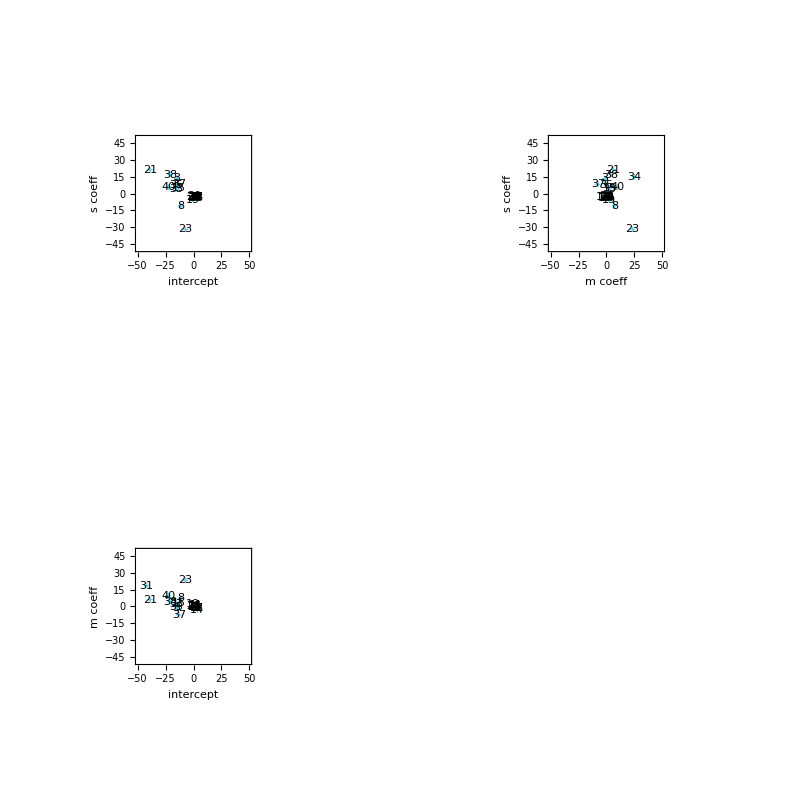

```mathematica
GraphicsGrid[{{plot[2],plot[3]},{plot[1],""}},Spacings->Auto]
```

```mathematica
expng[wd<>"kl1mean_zoom"]
```

C:\Users\pglpm\repositories\plinkinetti\matches_3_parameters\saved_data\kl1mean_zoom.png

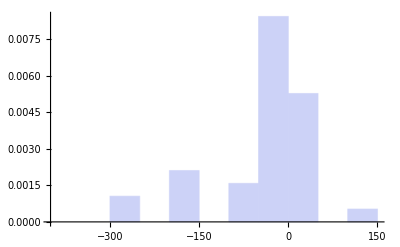

```mathematica
Histogram[data[[;;,2]],"FreedmanDiaconis","PDF",PlotRange->Auto]
```

```mathematica
ListPointPlot3D[data[[;;,2;;4]],BoxRatios->1,PlotStyle->PointSize[Large],PlotLabel->mylabels[{"JS-mean"}],ViewPoint->Dynamic[viewpoint]]
```

-Graphics3D-

```mathematica
expdf["plot_JS-mean"]
```

plot_JS-mean.pdf

```mathematica
data=Import[wd<>"points_js1mean.csv"];
```

```mathematica
data=Delete[10]@data;
```

```mathematica
data[[10,2;;4]]//MF
```

(Infinity
10
Infinity)

```mathematica
plot=ListPointPlot3D[data[[;;,2;;4]],BoxRatios->1,PlotStyle->PointSize[0.02],PlotLabel->mylabels[{"JS-mean"}],ViewPoint->Dynamic[viewpoint],PlotRange->All,AxesLabel->myaxes[{"intercept","m coeff","s coeff"}]];
```

```mathematica
Show[plot,Graphics3D[Text[#[[1]],1.04 #[[2;;4]]]&/@data]]
```

-Graphics3D-

```mathematica
expdf["plot_JS-mean"]
```

plot_JS-mean.pdf